#### 4.-2

For radioactive decay,

```mathematica
p [t_]:=λ ⅇ^(-λ t)
```

Taking the integral then yields

```mathematica
Integrate[p[tt], {tt, 0, t}]
```

1.-1. ⅇ^(-0.0229747 t)

This represents the probability that the atom has decayed by time t.

#### 4.-1

```mathematica
Integrate[x^a, {x, 0, 1}]
```

ConditionalExpression[1/(1+a),Re[a]>-1]

#### 4.0

```mathematica
D[(lambda^k Exp[-lambda])/(Factorial[k]), lambda]
```

(ⅇ^-lambda k lambda^(-1+k))/(k!)-(ⅇ^-lambda lambda^k)/(k!)

The derivative wrt. lambda of 1=Σ(λ^k e^(-λ)/k! is

```mathematica
0 ==  Sum[(ⅇ^-λ k λ^(-1+k))/(k!)-(ⅇ^-λ λ^k)/(k!), {k, 1, ∞}]
```

False

#### 4.1

The function x^a is bounded by [0,1], since 1^a = 1 for any a, and 0^a = 0 for any a.There is also no a for which this function is negative in this interval.

```mathematica
MCInt[a_,Ntries_] := Module[{j, x, y, nhit},
nhit = 0;
For[j = 0, j<Ntries, j++,
x = RandomReal[{0,1}];
y = RandomReal[{0,1}];
If[y < x^a, nhit++];
];
Return[nhit/Ntries];
]
```

```mathematica
MCInt[2,100000]
```

16617/50000

#### 4.2

```mathematica
ErrorTable[a_] := Module[{n, tries,mcval, expected, result},
result = Table[0, {x, 1, 7}];
expected[b_] := 1/(1+b);
For[n = 1, n≤ 7, n++,
tries = 10^n;
mcval = MCInt[a, tries];
result[[n]] = {tries,Abs[( expected[a] - mcval)/expected[a]]};
Print["Done w/ " <> ToString[n]];
];
Return[result];
]
```

```mathematica
tab05 = ErrorTable[0.5];
tab2 = ErrorTable[2.];
tab10 = ErrorTable[10.];
```

Done w/ 1

Done w/ 2

Done w/ 3

Done w/ 4

Done w/ 5

Done w/ 6

Done w/ 7

Done w/ 1

Done w/ 2

Done w/ 3

Done w/ 4

Done w/ 5

Done w/ 6

Done w/ 7

Done w/ 1

Done w/ 2

Done w/ 3

Done w/ 4

Done w/ 5

Done w/ 6

Done w/ 7

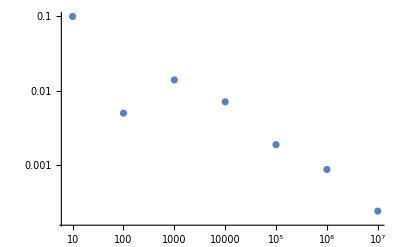

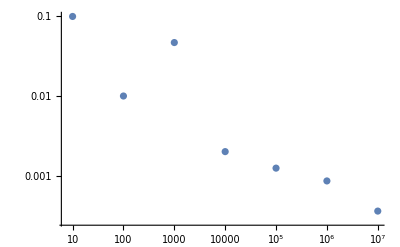

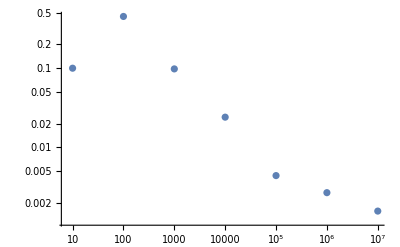

```mathematica
ListLogLogPlot[tab05]
ListLogLogPlot[tab2]
ListLogLogPlot[tab10]
```

The relationship between log(tries) and log(error) seems to follow a linear shape. However, the high variation in the data and the low number of datapoints means the relationship may not actually be linear.

#### 4.3

```mathematica
RadDecay[t_,λ_, Ntries_] := Module[{Nhit, n, x, y},
Nhit = 0;
p[T_,Λ_] := Λ Exp[-Λ T];
For[n= 0, n ≤ Ntries, n++,
x = RandomReal[{0,t}];
y = RandomReal[{0,λ}];
If[y < p[x,λ], Nhit++]
];
Return[(λ t)(Nhit/Ntries)];
]
```

1 half-life test :

```mathematica
RadDecay[2,N[Log[2]],1000]
```

0.723646

Cs-137:

```mathematica
γ = 30.17 (*years*);
λ = Log[2]/γ;
```

After 100 years (for example)

```mathematica
RadDecay[100, λ, 100000]
```

0.89668

U235 has a half-life of 703Myr, so in the age of the Earth, the probability that a U235 atom would have decayed is:

```mathematica
RadDecay[4, Log[2.]/0.703, 100000]
```

0.979635

Meanwhile, U238 has a half-life of 4.468Gyr, so the probability that a U238 atom would have decayed is

```mathematica
RadDecay[4, Log[2]/4.468, 100000]
```

0.461114

This is one of the reasons U238 is so much more common than U235 in nature.